```mathematica
(* Breusch=Pagan test for heteroskedasticity. *)
(* TODO: Load / add data files *)

(* Heteroscedastic? Perform Breusch-Pagan test. *)
(* 1. Fit a model. Fit hyperbolic power law function: *)
tc=.
numParams=4;
hyperbolicModel=a +(tc-ti)^m(b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])/.{c-> 0, d-> 0}
```

a+b (tc-ti)^m

```mathematica
(* Use the second (smaller) bubble: *)
bubble=2;
bubbleScaled=bubblesScaled[[bubble]];
```

```mathematica
(* Profiling over 0.1 < m < 0.9, 1. < tc < 3 months in the future *)
minM=0.1;
maxM=0.9;
months=3;
```

```mathematica
(* Try to estimate all the params using log-likelihood: *)
(* Define three months in the future scaled interval endpoint: *)
maxTc=(bubblesDays[[bubble]]+30 months)/bubblesDays[[bubble]]//N
```

1.43478

```mathematica
(* Define 1 week resolution scaled interval step: *)
stepTc=7/bubblesDays[[bubble]]//N
```

0.0338164

```mathematica
(* Define 10 days resolution scaled initial time step *)
stepTi=10/bubblesDays[[bubble]]//N
```

0.0483092

```mathematica
(* Fixed t1: *)
t1=1/3;
bubbleSelected=Select[bubbleScaled,#[[1]]>= t1&];
```

```mathematica
fit=Block[{},m=.;tc=.;
bestFit=MaximalBy[Flatten[Table[{tc,m,nlm=NonlinearModelFit[bubbleSelected,hyperbolicModel,{a,b}, ti];nlm["BestFitParameters"],
ℛ=nlm["FitResiduals"];
(* Fit an AR(1) process *)
ar1Process=ARProcess[μ,{ρ},σ^2];
estimatedAR1Model=FindProcessParameters[ℛ,ar1Process],
Total[ℛ^2]/(Length[ℛ]-numParams),
LogLikelihood[ar1Process/. estimatedAR1Model,ℛ]},{m,minM,maxM,1./10},{tc, bubbleScaled[[-1]][[1]]+0.0001, maxTc,stepTc}],1], Last]//Flatten[#, 1]&;modelParams=Join[bestFit[[3]], {Subscript[T, 1]-> t1,tc-> bestFit[[1]],m-> bestFit[[2]],LL-> bestFit[[6]], ℛerror-> bestFit[[5]]},bestFit[[4]]]]
```

{a→0.94402,b→-0.761599,T_1→1/3,tc→1.01171,m→0.5,LL→12857.2,ℛerror→0.0039695,ρ→0.995901,σ→-0.00569548,μ→-1.35509×10^-18}

```mathematica
tc=.
tf=tc/.fit[[4]]
```

1.01171

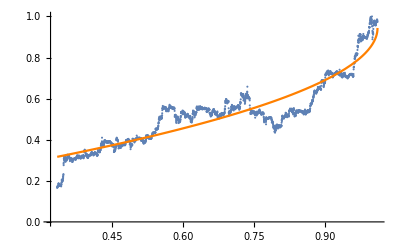

```mathematica
Show[ListPlot[bubbleSelected], Plot[Evaluate[hyperbolicModel/.fit], {ti, t1, tf}, PlotStyle->{Orange}, Evaluated->True]]
```

```mathematica
(* Fit the squared errors to a model with the same predictors :*)
(* 1. Fixing the fitted non-linear params *)
fitModel=hyperbolicModel/.fit[[4;;5]]
```

a+b (1.01171-ti)^0.5

```mathematica
ℛ2=nlm["FitResiduals"]^2;
newℛ2=Block[{newData=bubbleSelected},newData[[All,-1]]=ℛ2;newData];
```

```mathematica
nlm2=NonlinearModelFit[newℛ2,fitModel,{a,b}, ti]
```

FittedModel[0.0182463-0.0235648 (1.01171-ti)^0.5]

```mathematica
nlm2["BestFitParameters"]
```

{a→0.0182463,b→-0.0235648}

```mathematica
(* 2. Not fixing the non-linear params *)
fit3=Block[{},m=.;tc=.;
bestFit=MaximalBy[Flatten[Table[{tc,m,nlm3=NonlinearModelFit[newℛ2,hyperbolicModel,{a,b}, ti];nlm3["BestFitParameters"],
ℛ=nlm3["FitResiduals"];
(* Fit an AR(1) process *)
ar1Process=ARProcess[μ,{ρ},σ^2];
estimatedAR1Model=FindProcessParameters[ℛ,ar1Process],
Total[ℛ^2]/(Length[ℛ]-numParams),
LogLikelihood[ar1Process/. estimatedAR1Model,ℛ]},{m,minM,maxM,1./10},{tc, bubbleScaled[[-1]][[1]]+0.0001, maxTc,stepTc}],1], Last]//Flatten[#, 1]&;modelParams=Join[bestFit[[3]], {Subscript[T, 1]-> t1,tc-> bestFit[[1]],m-> bestFit[[2]],LL-> bestFit[[6]], ℛerror-> bestFit[[5]]},bestFit[[4]]]]
```

{a→0.0350274,b→-0.0385426,T_1→1/3,tc→1.01171,m→0.2,LL→18729.1,ℛerror→0.0000470947,ρ→0.990983,σ→-0.000918966,μ→-1.63657×10^-19}

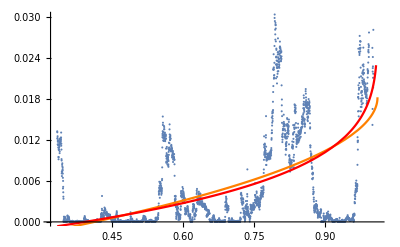

```mathematica
(* Plot *)
Show[ListPlot[newℛ2], Plot[{Evaluate[fitModel/.nlm2["BestFitParameters"]],Evaluate[hyperbolicModel/.fit3]}, {ti, t1, tf}, PlotStyle->{Orange, Red}, Evaluated->True]]
```

```mathematica
breuschPagan2=(Variance[ℛ2](Length[bubbleSelected]-1)-Total[nlm2["FitResiduals"]^2])/(2(Total[ℛ2]/Length[bubbleSelected])^2)
```

1238.53

```mathematica
breuschPagan3=(Variance[ℛ2](Length[bubbleSelected]-1)-Total[nlm3["FitResiduals"]^2])/(2(Total[ℛ2]/Length[bubbleSelected])^2)
```

980.596

```mathematica
(* Compute the p-value: *)
1-CDF[ChiSquareDistribution[Length[nlm["BestFitParameters"]]-1],breuschPagan3]
```

0.